Last modified on: Tuesday, July 10, 2018 at 23:13

Author Info

Sumner Magruder

Markus van Almsick

University of Hamburg

Poster Session Content

A deviation from “Try to Use Neural Nets for Graph Isomorphism”

Find an input form of Graphs that are sufficient for Neural Networks to learn on.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

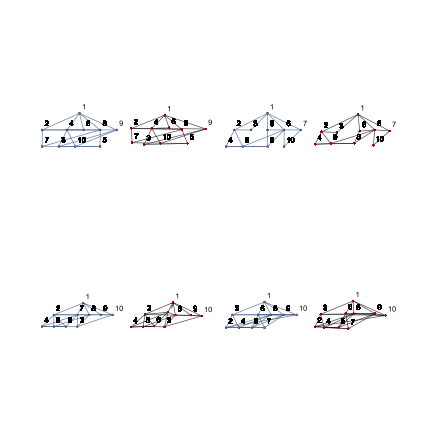

Despite sparsity, it seems that the Adjacency Matrix is sufficient for learning complex and even arbitrary properties of Graphs

Explore other input formats.
Export other graph properties.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

What is a graph?

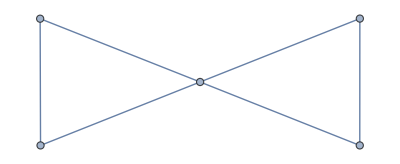
Vertices and edges
{1<->2,1<->5,2<->3,2<->4,2<->5,3<->4}

Can be represented as an adjacency matrix (left) or graphically (right)
(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0)-Graphics--Graphics-

What does it take to draw a layered graph?

To draw a layered graph, generally the following steps are performed:
	1. convert input graph - G(V, E) - to a directed acyclic graph (DAG) - G(V, A)
		find the strongly connected components
		find the minimum feedback-arc-set / feedback set and remove / reverse edges accordingly
	2. layer the resultant DAG - G(V, A, L)
		most likely some variant of longest-path
	3. ensure the layered DAG is properly layered by injecting placeholder “dummy” vertices and edges
		Sugiyama approach
	4. order each layer by performing bi-partite edge crossing minimization in several up / down sweeps
		without testing every combination, at worse ≈1.63 times the minimum number of crossings
	5. construct a block-graph from the ordered-layered directed acyclic graph
	6. calculate x-coordinates
	7. calculate y-coordinates
	8. render graphics

Can we take the adjacency matrix for the graph and skip from step 1 to step 8?

Coordinates (output) are taken from the input graph on the (left in blue) and after training we can, from the adjacency matrix (input) get the coordinates of the vertices (right in black and red)

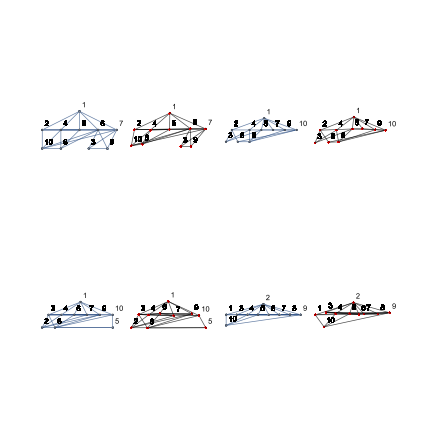
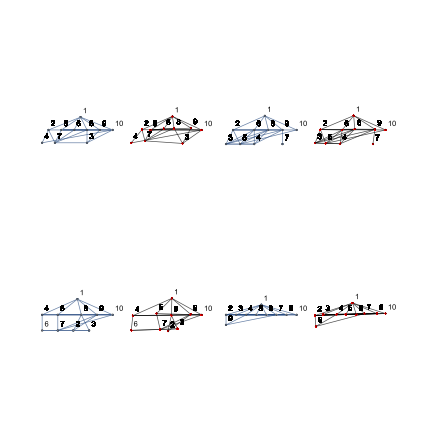

Does this address Graph Isomorphism?

Kind of.  As isomorphic graphs are often rendered the same way.

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Five neural networks:
	1. detecting whether or not a graph is simple
	2. a fully-connected NN for predicting Layered embedding coordinates
	3. a CNN for predicting Layered embedding coordinates
	4. a fully-connected NN for predicting Spring Electrical Embedding embedding coordinates
	5. a CNN for predicting Spring Electrical Embedding embedding coordinates
	
of which the linear networks outperform the CNNs, and LayeredEmbedding performs better than SpringElectricalEmbedding

#### Code

Provide one of:

https://github.com/SumNeuron/WSS2018

#### Conclusions in Detail

Why some architectures or embeddings are more easily learned is unclear. 
However, a non-trivial task - graph drawing - seems to be learn-able.

#### All Visualizations

#### Data Sources Links/References

http://community.wolfram.com/groups/-/m/t/1373118

#### Future Directions

Try different NN architectures
Try different Graph Embeddings
Try using an LSTM where vertices are embedded as characters and walks are feed in
Try using all Graph Embeddings simulatenously

#### Background Info Links/References

#### Keywords

Provide keywords as items

Graph

GraphLayout

NeuralNetwork

Visualization

#### Other information